# Dave Meretzky DGFEM 1D Heat Equation

## Geometry

```mathematica
n = 128;
elements = {};
For[i = 1, i ≤ n/4, i++1,
AppendTo[elements, {i, i-1, i}]
];
elements
```

{{1,0,1},{2,1,2},{3,2,3},{4,3,4},{5,4,5},{6,5,6},{7,6,7},{8,7,8},{9,8,9},{10,9,10},{11,10,11},{12,11,12},{13,12,13},{14,13,14},{15,14,15},{16,15,16},{17,16,17},{18,17,18},{19,18,19},{20,19,20},{21,20,21},{22,21,22},{23,22,23},{24,23,24},{25,24,25},{26,25,26},{27,26,27},{28,27,28},{29,28,29},{30,29,30},{31,30,31},{32,31,32}}

## Polynomials

```mathematica
ϕ[k_,j_, x_] :=(-1)^(j+1)* (Mod[j,2]+k) + (-1)^j*x;
```

## Analysis

## M matrix

```mathematica
M =  ConstantArray[0,{n,n}];
Minv =  ConstantArray[0,{n,n}];
p1 = 0;
p2 = 0;


For[k =0, k ≤ n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

M[[2k+i,2k+j]] += ∫_p1^p2 ϕ[k,j, x]*ϕ[k,i, x]ⅆx;
Minv[[2k+i,2k+j]] += ∫_p1^p2 ϕ[k,j, x]*ϕ[k,i, x]ⅆx;
If[j ==i,
Minv[[2k+i+n/2,2k+j+n/2]] += 1
];

];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
MatrixForm[M];
Minv = Inverse[Minv];
```

```mathematica
MatrixForm[Minv];
```

## M bar, K bar, and K to K matrix

```mathematica
K=  ConstantArray[0,{n,n}];
p1 = 0;
p2 = 0;
(*__________________________________kbar matrix________________________*)


For[k =0, k ≤  n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

K[[2k+i,n/2+2k+j]] +=-∫_p1^p2 ϕ[k,j, x]*D[ϕ[k,i, x], x]ⅆx


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
(*__________________________________mbar matrix________________________*)
For[k =0, k ≤  n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

K[[2k+i+n/2,n/2+2k+j]] += ∫_p1^p2 ϕ[k,j, x]*ϕ[k,i, x]ⅆx


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
(*__________________________________k matrix________________________*)
For[k =0, k ≤  n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

K[[2k+i+n/2,2k+j]] +=∫_p1^p2 ϕ[k,j, x]*D[ϕ[k,i, x], x]ⅆx


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
init = ConstantArray[0,n];
(*K[[n/2+1]] = init;
K[[n]] = init;
K[[n/2+1,9]] = 1;
K[[n/2+2,1]] = 0;
K[[n,n]] = 1;*)
MatrixForm[K];
```

## Flux matrix

```mathematica
Flux=  ConstantArray[0,{n,n}];
p1 = 0;
p2 = 0;


For[k =0, k ≤  n/4 -1,++k, (* iterate over the elements, test func, functions, *)
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++, 

p = elements[[k +1, j+1]] ; (* p is the node dual to the j functions *)


(*____________________b flux for σ terms___________________________
upper right hand side, gets dotted with b's 


*)
If[j == 1, (* 
if j = 1, then k-1 j=2 polynomial and the k j=1 
polynomial of the kth element are collapsed onto their dual and placed k, bj = 1 column but the k-1, i = 2 th row.  
*)
If[2k+i-1>0,(* make sure that you dont go out the top of the matrix*)
Flux[[2k+i-1,n/2+2k+j]] +=1/2 *  ϕ[k-1,j+1, p]*ϕ[k,i, p];
];
Flux[[2k+i,n/2+2k+j]] +=1/2 *  ϕ[k,j, p]*ϕ[k,i, p];
];

(* if j = 2 then the k=1, j=2 and k+1, j=1 polynomials collapse together*)


If[j == 2,

Flux[[2k+i,n/2+2k+j]] +=1/2 *  ϕ[k,j, p]*ϕ[k,i, p];
If[2k+i+1 < n/2, (*make sure you dont go out right hand edge *)
Flux[[2k+i+1,n/2+2k+j]] +=1/2 *  ϕ[k+1,j-1, p]*ϕ[k,i, p];
];
];

(*______________________a flux for u terms_______________________*);
If[j == 1,
If[2k+i-1 + n/2>n/2,(*make sure you dont go into 8th row*)
Flux[[2k+i-1 + n/2,2k+j]] +=-1/2 *  ϕ[k-1,j+1, p]*ϕ[k,i, p];
];
Flux[[2k+i +n/2,2k+j]] +=-1/2 *  ϕ[k,j, p]*ϕ[k,i, p];
];

If[j == 2,

Flux[[2k+i+n/2,2k+j]] +=-1/2 *  ϕ[k,j, p]*ϕ[k,i, p];

If[2k+i+1 +n/2<n,(*make sure you dont go into 8th column*)
Flux[[2k+i+1 +n/2,2k+j]] +=-1/2 *  ϕ[k+1,j-1, p]*ϕ[k,i, p];
];
];


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
MatrixForm[Flux];
```

## -(mbarinv k) matrix

```mathematica
Mbarb=  ConstantArray[0,{n/2,n/2}];
Kb=  Flux[[n/2+1;;n, 1;;n/2]];


(*____________________Mbarb_____________________________*)
For[k =0, k ≤  n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

Mbarb[[2k+i,2k+j]] += ∫_p1^p2 ϕ[k,j, x]*ϕ[k,i, x]ⅆx


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
(*_______________________Kb_____________________________*)
For[k =0, k ≤  n/4 -1,++k, 
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;
For[i = 1, i ≤ 2, i++,
For[j = 1, j ≤ 2, j++,

Kb[[2k+i,2k+j]] +=∫_p1^p2 ϕ[k,j, x]*D[ϕ[k,i, x], x]ⅆx


];      (* end test function loop, rows*)
];  (* end test function loop, rows*)
]; (* end element loop *)
```

## Initial condition

```mathematica
init = ConstantArray[0,n];
init[[30;;40]] = 20;
init[[n/2+1;;n]] = 1;
init
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20,20,20,20,20,20,20,20,20,20,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## Linear System, Inversion, timestepping:

```mathematica
steps = {};

For[t = 0, t≤ 100, t++,
plts = {};
For[k = 0, k ≤  n/4 -1, k++,
p1 = elements[[k+1 , 2]] ;
p2 = elements[[k +1, 3]] ;

If[k == 0,
a1 = init[[(2*k+1)]];
];

If[k == n/4 -1,
a2 = init[[(2*k+2)]];
];

If[k != 0,
a1 = .5*(init[[(2*k+1)]]+init[[2*k]]);
];

If[k != n/4-1,
a2 = .5*(init[[(2*k+2)]]+init[[2*k+3]]);
];

AppendTo[plts,Plot[


a1*ϕ[k,1, x] +  a2*ϕ[k,2, x],

 {x, p1, p2}]

];
];
AppendTo[steps, plts];

If[t ≠0, 
init[[n/2+1;;n]] = -1*Inverse[Mbarb].Kb.init[[1;;n/2]]
];

ab = Minv.(K-Flux).init;

init =  init + .0001* ab;
];
```

## Visualization

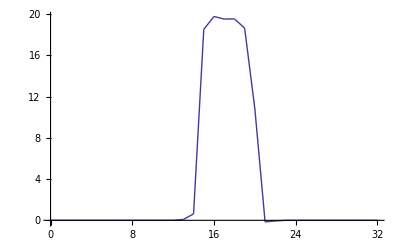

```mathematica
Show[steps[[1;;100]], PlotRange -> All]
```